```mathematica
SetDirectory[NotebookDirectory[]];
```

## p10q3

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
```

```mathematica
datadir="../Processed_Data/8_FiniteSizeAnalysis_CDW";
```

```mathematica
a0v0d4small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d4small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.4_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d4small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.6_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d44small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0_amag1_V0.44_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d44small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.4_amag1_V0.44_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d44small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.6_amag1_V0.44_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d5small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d5small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.4_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d5small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n3a0.6_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d4large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d4large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.4_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d4large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.6_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d44large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0_amag1_V0.44_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d44large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.4_amag1_V0.44_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d44large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.6_amag1_V0.44_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d5large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d5large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.4_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d5large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p10q3n4a0.6_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
nsmall={0,1,2};
nlarge={0,1,2,3};
```

```mathematica
psize=0.03;
lthickness=0.006;
```

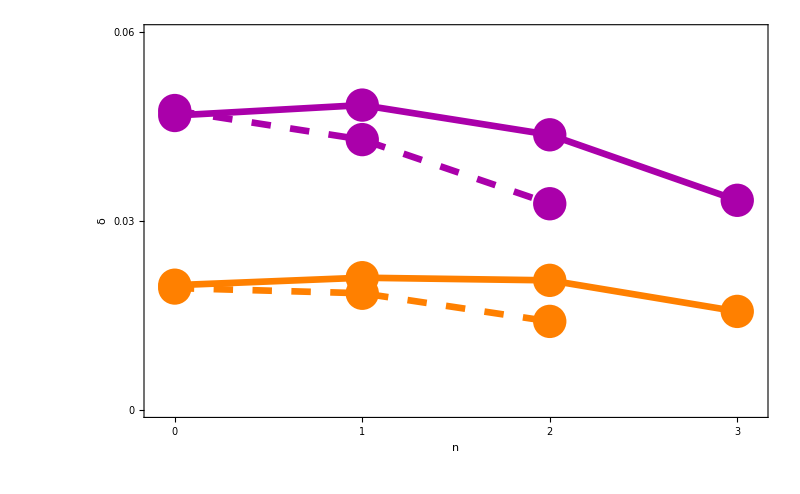

```mathematica
xrange={-0.1,3.1};
yrange={0,0.06};
Show[
ListPlot[Transpose@{nsmall,a0v0d4small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v0d4small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v0d4large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v0d4large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0v0d5small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v0d5small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v0d5large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v0d5large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.03,0.06},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

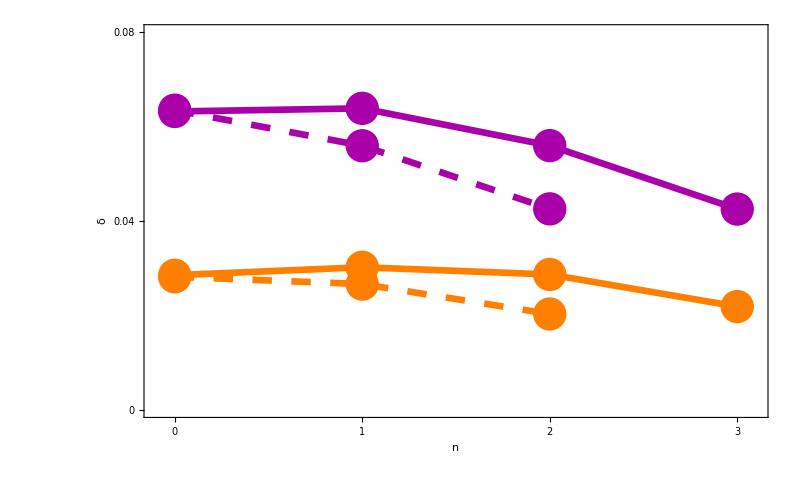

```mathematica
xrange={-0.1,3.1};
yrange={0,0.08};
Show[
ListPlot[Transpose@{nsmall,a0d4v0d4small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v0d4small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v0d4large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v0d4large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d4v0d5small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v0d5small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v0d5large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v0d5large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.04,0.08},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

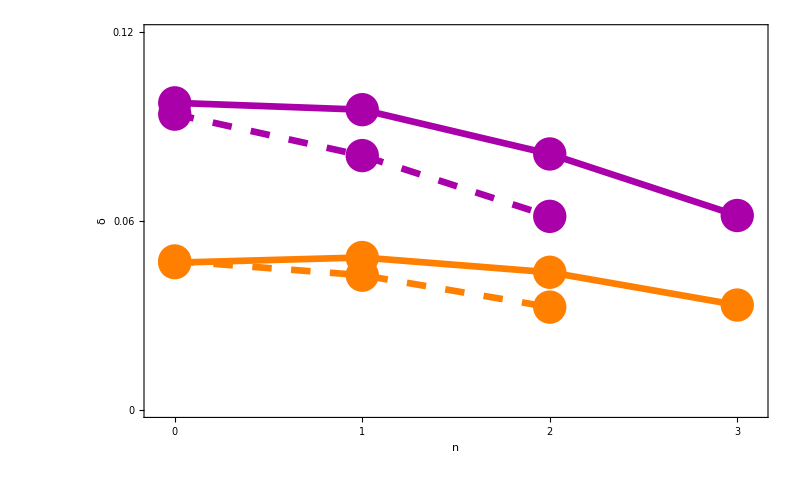

```mathematica
xrange={-0.1,3.1};
yrange={0,0.12};
Show[
ListPlot[Transpose@{nsmall,a0d6v0d4small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v0d4small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v0d4large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v0d4large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d6v0d5small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v0d5small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v0d5large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v0d5large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.06,0.12},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

## p14q3

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
```

```mathematica
datadir="../Processed_data/8_FiniteSizeAnalysis_CDW";
```

```mathematica
a0v0d3small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0_amag1_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d3small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0.4_amag1_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d3small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0.6_amag1_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d4small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d4small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0.4_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d4small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0.6_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d5small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d5small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0.4_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d5small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n2a0.6_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d3large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0_amag1_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d3large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0.4_amag1_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d3large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0.6_amag1_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d4large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d4large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0.4_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d4large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0.6_amag1_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d5large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d5large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0.4_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d5large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/p14q3n3a0.6_amag1_V0.5_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
nsmall={0,1};
nlarge={0,1,2};
```

```mathematica
psize=0.03;
lthickness=0.006;
```

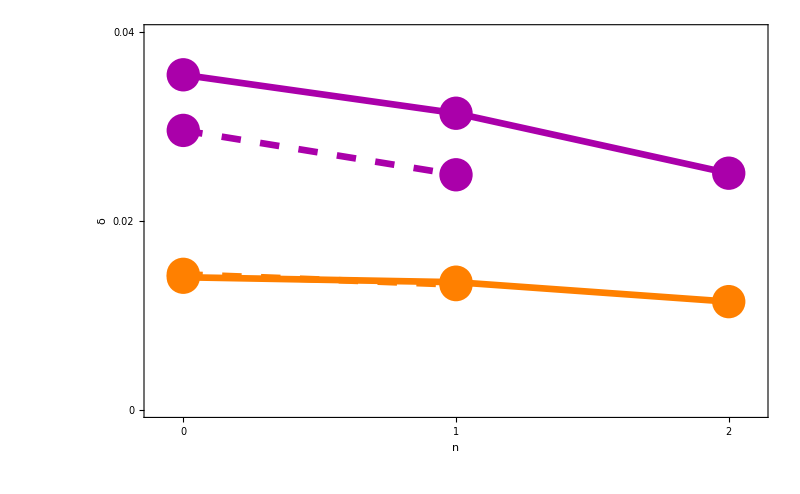

```mathematica
xrange={-0.1,2.1};
yrange={0,0.04};
Show[
ListPlot[Transpose@{nsmall,a0v0d4small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v0d4small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v0d4large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v0d4large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0v0d5small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v0d5small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v0d5large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v0d5large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.02,0.04},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

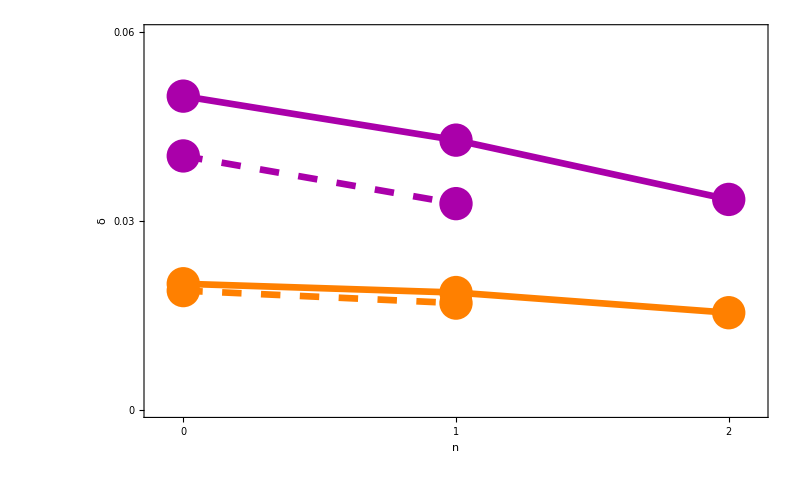

```mathematica
xrange={-0.1,2.1};
yrange={0,0.06};
Show[
ListPlot[Transpose@{nsmall,a0d4v0d4small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v0d4small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v0d4large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v0d4large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d4v0d5small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v0d5small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v0d5large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v0d5large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.03,0.06},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

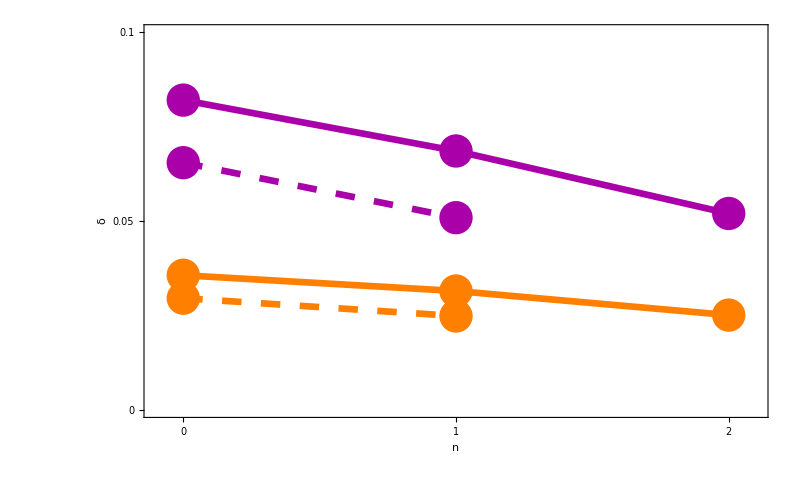

```mathematica
xrange={-0.1,2.1};
yrange={0,0.1};
Show[
ListPlot[Transpose@{nsmall,a0d6v0d4small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v0d4small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v0d4large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v0d4large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d6v0d5small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v0d5small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v0d5large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v0d5large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.05,0.1},None},{{0,1,2,3},None}},FrameTicksStyle->FontSize->50
]
```

## Honeycomb

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
```

```mathematica
datadir="../Processed_Data/8_FiniteSizeAnalysis_CDW";
```

```mathematica
a0v0d3small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0_amag0.5_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d3small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0.4_amag0.5_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d3small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0.6_amag0.5_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d4small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0_amag0.5_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d4small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0.4_amag0.5_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d4small=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl19a0.6_amag0.5_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d3large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0_amag0.5_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d3large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_amag0.5_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d3large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0.6_amag0.5_V0.3_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
a0v0d4large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0_amag0.5_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d4v0d4large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_amag0.5_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
a0d6v0d4large=(Transpose@Re[Map[cstn,Import[StringJoin[datadir,"/honeycombOBC_nl20a0.6_amag0.5_V0.4_CDWGenerationTrend.txt"],"Data"]]])[[1]];
```

```mathematica
nsmall=Range[0,18,1];
nlarge=Range[0,19,1];
```

```mathematica
psize=0.03;
lthickness=0.006;
```

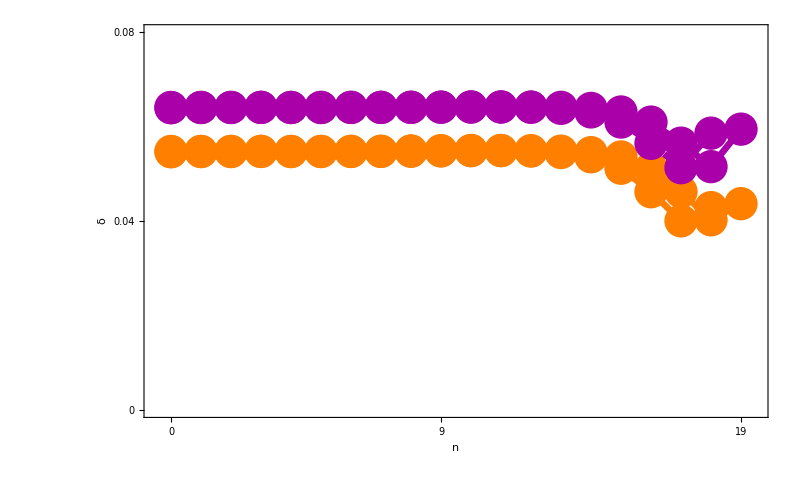

```mathematica
xrange={-0.5,19.5};
yrange={0,0.08};
Show[
ListPlot[Transpose@{nsmall,a0v0d3small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v0d3small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v0d3large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v0d3large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0v0d4small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0v0d4small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0v0d4large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0v0d4large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.04,0.08},None},{{0,9,19},None}},FrameTicksStyle->FontSize->50
]
```

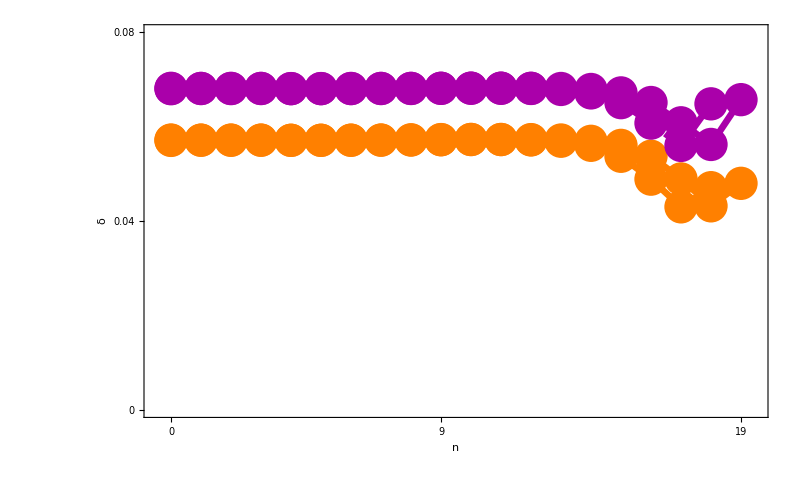

```mathematica
xrange={-0.5,19.5};
yrange={0,0.08};
Show[
ListPlot[Transpose@{nsmall,a0d4v0d3small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v0d3small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v0d3large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v0d3large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d4v0d4small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d4v0d4small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d4v0d4large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d4v0d4large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.04,0.08},None},{{0,9,19},None}},FrameTicksStyle->FontSize->50
]
```

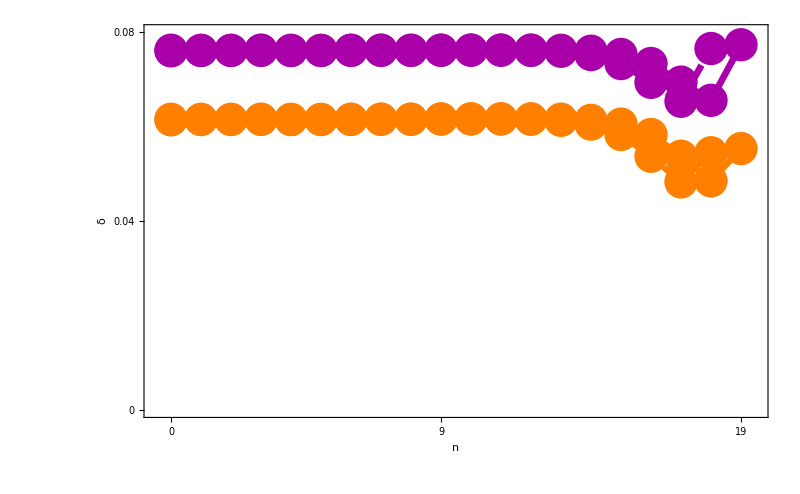

```mathematica
xrange={-0.5,19.5};
yrange={0,0.08};
Show[
ListPlot[Transpose@{nsmall,a0d6v0d3small},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v0d3small},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v0d3large},PlotStyle->{Orange,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v0d3large},Joined->True,InterpolationOrder->1,PlotStyle->{Orange,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nsmall,a0d6v0d4small},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nsmall,a0d6v0d4small},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness],Dashing[Large]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{nlarge,a0d6v0d4large},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{nlarge,a0d6v0d4large},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"n\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.04,0.08},None},{{0,9,19},None}},FrameTicksStyle->FontSize->50
]
```